```mathematica
SetOptions[InputNotebook[],AutoGeneratedPackage->None];
left::usage = "Tag for disk copies outside of cylinder";
right::usage = "Tag for disk copies outside of cylinder";
hat::usage = "Tag for disk copies outside of cylinder";
```

```mathematica
(* get the radius function right *)
```

## Styles and files

```mathematica
runsToGenerate  = {};
```

```mathematica
githubPath= PersistentSymbol["persistentGitHubPath","Local"];
AppendTo[$Path,FileNameJoin[{githubPath,"Packages"}]];
Needs["LatticePhyllotaxis`"];
Needs["DiskStacking`"];
Get["scpPaperStylings.m"]
```

```mathematica
gDrive = PersistentSymbol["persistentGDrive"];
runDirectory = FileNameJoin[{gDrive,"Work\\Textbook\\Stacked coin paper\\Mathematica\\Runs"}];
eSetDirectory = (* post processed runs, no real reason for this to be different from runDirectory *) FileNameJoin[{gDrive,"Work\\Textbook\\Stacked coin paper\\Mathematica\\Esets"}];

draftFigureDirectory = FileNameJoin[{gDrive,"Work\\Textbook\\Stacked coin paper\\DraftFigures"}];


getRunByTag[tag_] := Module[{file},
file = FileNameJoin[{runDirectory,StringJoin[tag,".mx"]}];
If[FileExistsQ[file],Return[Import[file]]];
Print["Can't load ", tag, " from ", file];
Abort[]
];
```

```mathematica
jParastichyColour[n_] := jStyle["ParastichyColour"][n];
jFont[n_] := {FontFamily->  jStyle["FontFamily"],FontSize-> n};
paraColours= <|Red-> jParastichyColour[1],Blue-> jParastichyColour[2]|>;
leftRightColours = <|"Left"-> jParastichyColour[1],"Right"-> jParastichyColour[2]|>;
jBaseStyle= jFont[12];

SetAttributes[jExport,HoldFirst];

jExport[fig_] := Module[{figname},
SetDirectory[draftFigureDirectory];
figname=SymbolName[Unevaluated[fig]];
Export[StringJoin[figname,".jpg"],fig,ImageResolution->300];Export[StringJoin[figname,".pdf"],fig,ImageResolution->300];
ResetDirectory[];
fig
];
```

## Multirun code

```mathematica
doOneRun[parameters_] := Module[{run},
run = DiskStacking`runFromLattice[parameters["Lattice"]];
run= readyRunFromParameter[run,parameters] ; 
run=doMonitoredRun[run];
saveRunByTag[run];
run
];

restartOneRun[lastRun_] := Module[{run},
run=lastRun;
run = DiskStacking`restartRunFromRun[run];
run= readyRunFromParameter[run,lastRun["Arena"]] ; 
run=doMonitoredRun[run];
saveRunByTag[run];
run
]

doMonitoredRun[run_] := Module[{res},
SeedRandom[run["Arena"]["Run"]];
res=run;
monitorRun= res["Arena"]["Run"];
monitorPP = <|"Noise"->res["Arena"]["Noise"],"rSlope"->res["Arena"]["rSlope"]|>;
res = DiskStacking`executeRun[res]; 
res 
];


saveRunByTag[run_] :=  Module[{parameters,saveFile,saveRun,tag},
parameters=run["Arena"];
tag=parameters["Tag"];
If[MissingQ[tag],tag="runData"];
saveFile= FileNameJoin[ {runDirectory,tag <> ToString[parameters["Run"]] <> ".mx"}];
saveRun =<|"File"->saveFile,"Run"->run|>;
Export[saveFile,saveRun];
run
];


doRunSets[parameterSets_] := Module[{res,abortCheck,runSets,timing},
abortCheck[parameterSet_] := CheckAbort[doOneRun[parameterSet],Print["Abort running ",parameterSet["Run"]]; Missing[parameterSet["Run"]]];
monitorRunTotal = Length[parameterSets];
monitorRunNumber= 0;
{timing,res}= Timing[Monitor[runSets=Map[(monitorRunNumber++;abortCheck[#]&),parameterSets],{monitorRunTotal,monitorRunNumber,monitorRun,monitorPP}];];
runSets
];


runExtractNonOverlappingChains[file_] := Module[{res},
monitorFile=file;
res=Import[file]["Run"];
DiskStacking`postRunExtractNonOverlappingChains[res]
];
```

```mathematica
latestRadius[run_] := Last@Values[DiskStacking`runDisksRadius[run]];
latestCentre[run_] := Last@Values[DiskStacking`runDisksHeight[run]];

readyRunFromParameter[lastrun_,experimentParameters_] := Module[{runParameters,run,arena,initialRadius,finalRadius,initialZ,makef,finalZ,showArena},

(* set defaults *)
runParameters= <|
"rScale"->10,
"rSlope"->0.03,
"power"-> 1,
"Lattice"->LatticePhyllotaxis`latticeOrthogonal[{0,1}],
"zMax"->Missing[],
"runNumber"->1,
"diskMax"->∞,
"PostFixChains"->0,
"Run"->"",
"Noise"->Missing[]
|>;

runParameters= Append[runParameters,experimentParameters];
run=lastrun;
run["Arena"] = createArena[run,runParameters];
run
];
(*
restartRunFromParameters[run_,runParameters_] := Module[{res},
(* strip out all but the top chain*)
res = DiskStacking`restartRunFromRun[run];
res["Arena"] = createArena[res,runParameters];
res
];*)


createArena[run_,runParameters_] := Module[{arena,initialRadius,finalRadius,initialZ,makef,finalZ,showArena},

(* create the r Function *)
initialRadius=latestRadius[run];
initialZ =  latestCentre[run];
finalRadius= initialRadius/runParameters["rScale"];

makef=powerFunctionProperties[ {initialRadius,finalRadius},runParameters["rSlope"],initialZ,
runParameters["power"]];
finalZ = makef["zEnd"];

arena=KeyDrop[runParameters,{"Lattice"}];
arena["rFunction"]= makef["Function"];
arena["zMax"]= finalZ + runParameters["PostFixChains"]* 4* finalRadius;
arena
];

powerFunctionProperties[ {rStart_,rEnd_},rSlope_,zStart_,power_] := Module[{zSlopeRange,zEnd,f,rDash,scaler},
rDash = -rSlope;
scaler = Sign[rDash]*(Abs[(zEnd-zStart) * rDash] )^ (power-1);
zEnd = zStart + ( (rEnd-rStart))/rDash ;

f = Function[{z}, rStart+ Piecewise[ {
{0,z< zStart}
,{(((z-zStart) * Abs[rDash])^power)/scaler, z< zEnd}
, { (((zEnd-zStart) *Abs[ rDash] ))^power/scaler,True}
}]];
f = functionClosure[f];
<|"Function"-> f, "zEnd"-> zEnd|>
]

functionClosure[f_] := Function[{z$},Evaluate[f[[2]]]]
```

## 2 fig:scpNonOpposed Illustrative lattice plot

```mathematica
scpShowParastichyLines[lattice_,lineColourFunction_]  :=  Module[{ll,llines,paraset,plines,numbers,rise,divergence,glines},
ll =Take[Flatten[ LatticePhyllotaxis`latticeLabel[lattice]],2];
llines = Map[LatticePhyllotaxis`latticeParastichyLines[lattice,#]&,ll];
numbers= KeyValueMap[Style[Text[#1,#2],Background->White]&,KeyTake[lattice["namedLatticePoints"],Range[0,10]]];
rise= Translate[Arrow[{{lattice["namedLatticePoints"][1][[1]],lattice["namedLatticePoints"][0][[2]]},lattice["namedLatticePoints"][1]}],{0.05,0}];
divergence= {Arrow[{lattice["namedLatticePoints"][0],{lattice["namedLatticePoints"][1][[1]],lattice["namedLatticePoints"][0][[2]]}}]};
glines = {Line[{{-1/2,lattice["namedLatticePoints"][0][[2]]},{1/2,lattice["namedLatticePoints"][0][[2]]}}],
,Line[{{-1/2,lattice["namedLatticePoints"][1][[2]]},{1/2,lattice["namedLatticePoints"][1][[2]]}}]};
Graphics[{
{jStyle["CylinderColour"],LatticePhyllotaxis`latticeGraphicsCylinder[lattice]}
,{FaceForm[White],LatticePhyllotaxis`latticeCircles[lattice]/. Circle->Disk},
,{Thin,Gray,glines}
, {Thick,MapIndexed[{lineColourFunction[First[#2]],#1}&,llines]}
,{PointSize[Small],Point[LatticePhyllotaxis`latticePoints[lattice]]}
,Arrowheads[0.02],rise,divergence,
,numbers
,Text["Divergence d",{0.2,0},{0,1.5},Background->White]
,Text["Rise h",{0.5,0.022},{-1.1,0},Background->White]
},PlotRange->{{-1/2,.6},{-0.05,0.4}}
,BaseStyle->Directive[FontFamily-> jStyle["FontFamily"],FontSize->Scaled[0.03]]
]
];

scpNonOpposed := Module[{lattice,dh},
dh=LatticePhyllotaxis`latticeDivergenceRiseForNonOpposedTC[{2,5}];
lattice = LatticePhyllotaxis`latticeFromDivergenceRise[dh, {-0.1,0.5}];

Legended[scpShowParastichyLines[lattice,jParastichyColour],LineLegend[{jParastichyColour[1],jParastichyColour[2]},{"2-parastichies","5-parastichies"},LabelStyle->Directive[FontFamily-> jStyle["FontFamily"],FontSize->Scaled[0.015]]]]
];
```

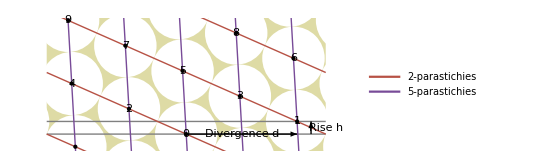

```mathematica
jExport[scpNonOpposed]
```

## 3 fig : scpVanIterson

```mathematica
viSwatch = <| "TouchingCircle"->  jParastichyColour[1]
,"OpposedTouchingCircle"-> jParastichyColour[1]
,"NonOpposedTouchingCircle"->jStyle["CylinderColour"]
,"FibonacciBranch"-> jParastichyColour[1]
,"NonFibonacciBranch"-> jStyle["CylinderColour"]
,"NonTouchingCircle"-> LightGray |>;

panelLabelBothSides [mn_,at_,scaling_:0.08] := Module[{obj,reflect},
reflect[{x_,y_}] := {1-x,y};
{panelLabel[mn,at,scaling],panelLabel[mn,reflect[at],scaling]}
];

panelLabel [{m_,n_},at_,scaling_:0.08] := Module[{textsize,obj},
textsize[{x_,y_}] := Scaled[scaling * Min[Sqrt[y],0.5]];
obj=Grid[
{{Style[StringTemplate["``,``"][m,n],jFont[textsize[at]]]}}
,Frame->None
];
Inset[obj,at]
];

scpTreePlot[mnPairs_,labelPairs_,scaling_,opts:OptionsPattern[]] := Module[{linelabels,hmax,plotRange,boundaries},

linelabels := Map[touchingCircleLabel,labelPairs];

hmax = 1.2;
plotRange = PlotRange  /. List@opts;

boundaries = {
{Thick,LightGray,Map[LatticePhyllotaxis`vanItersonTouchingCirclePrimaryNonOpposed,mnPairs]/. ∞-> plotRange⟦2,2⟧}
,{Thick,viSwatch["TouchingCircle"],Map[LatticePhyllotaxis`vanItersonTouchingCirclePrimaryOpposed,mnPairs]}
};
Graphics[
{  
{LightGray,Line[{{1,0},{1,hmax}}]}
,{boundaries}
,linelabels
},
Evaluate[FilterRules[{opts}, Options[Graphics]]]
]
];

pairsTodo[hmin_,imax_] := Module[{n,ntodo,hm,res,makeP},
ntodo[m_,hm_] := Ceiling[Sqrt[m^2+ 1/hm]];
makeP[i_,hm_] := Select[Table[{i,j},{j,i+1,ntodo[i,hm]}],CoprimeQ[i,#[[2]]]&];
res= Select[ Table[makeP[i,hmin],{i,imax}],Length[#]>0&];
res=Flatten[res,1];
res
];

 addSubTree[mnpairs_] := DeleteDuplicates@Flatten[Map[ {#,{#⟦1⟧,#⟦1⟧+#⟦2⟧},{#⟦2⟧,#⟦1⟧+#⟦2⟧}}&,mnpairs],1];

touchingCircleLabel[labelAssociation_] := Module[{mn,at,m,n,str1,gr,posx,posy},
mn= labelAssociation["Pair"];
{posx,posy}= labelAssociation["Position"];
If[posx=="Left",posx=1];
If[posx=="Right",posx=-1];
{m,n}= mn;
at =LatticePhyllotaxis`vanItersonRegionPoints[mn]["TouchingCircle"];
If[posy=="Terminal",at[[2]]= 0;posy=1];
str1 = Style[StringTemplate["``,``"][m,n],Background->None,jFont[12]];
gr  = Text[str1,at,{posx,posy}];
gr
];
```

```mathematica
dh=LatticePhyllotaxis`latticeDivergenceRiseForNonOpposedTC[{2,5}];
nop25= N@ dh;

scpviTree := Module[{mnPairs,labelPairs,xcut,ymax},
mnPairs  = {{2,3},{2,5},{2,7},{3,4},{3,5},{3,8},{5,7},{5,8},{3,11},{8,11},{5,13},{8,13},{5,12},{7,12},{2,9},{7,9}};
labelPairs= {
<|"Pair"->{2,3},"Position"->{-2,-1}|>,
<|"Pair"->{2,5},"Position"->{-1,-1}|>,
<|"Pair"->{3,5},"Position"->{1,-1}|>,
<|"Pair"->{5,8},"Position"->{-1.2,-1.}|>,
<|"Pair"->{4,5},"Position"->{-2,-1}|>,
<|"Pair"->{2,7},"Position"->{-2.5,0}|>,
<|"Pair"->{5,7},"Position"->{1.5,0}|>,
<|"Pair"->{3,8},"Position"->{1.5,-.5}|>
};
xcut={0.348,0.45};
ymax =0.075;
Legended[Show[{scpTreePlot[ mnPairs,labelPairs,0.24
,PlotRange->{xcut,{-0.0,ymax}}
,Axes->True,AxesOrigin->{xcut[[1]],-0.0}
,AxesLabel->{"Divergence d","Rise h"},BaseStyle->jFont[12]
,Ticks->{{0.35,0.4,0.45},{0,0.025,0.05,0.075}}
,AspectRatio->Automatic
,PlotRangeClipping->True
,ImageSize->400
],
Graphics[{jParastichyColour[3],PointSize[Medium],Point[nop25]}]}],Placed[LineLegend[{Directive[Thick,LightGray],{Thick,viSwatch["TouchingCircle"]}},{"Non-opposed disk-lattices","Opposed disk-lattices"},LabelStyle->Directive[jFont[12]]],Scaled[{0.75,.9}]]
]
]
```

```mathematica
(*scpVanIterson= GraphicsRow[{Image[viImage,ImageSize->150],scpviTree},ImageSize->550];
*)
scpVanIterson=Show[scpviTree,ImageSize->400];

jExport[scpVanIterson]
```

$Aborted

scpVanIterson

## 5 and 8 fig:scpDeterministicTransition and fig:scpParastichyCountsTo55

### Code to build upto55

```mathematica
expandParameterSets[parameterListAssociation_] := Module[{res,runCount=1,parameterNames,parameterLists,labelParameter},
parameterNames= Keys[parameterListAssociation];
parameterLists = Values[parameterListAssociation];
labelParameter[parameterList___] := Append[Association@Thread[parameterNames ->{parameterList}],"Run"->runCount++];
res=Flatten[Outer@@ Prepend[parameterLists,labelParameter]]
];
```

```mathematica
makescpParaTransitions55[] := (
pto55= expandParameterSets[<|"Tag"->{"scp-upto55-solo"},"rSlope"->{0.03},"rScale"->{60},"PostFixChains"->{2},
"Noise"->Join[{0}],
"Lattice"->{LatticePhyllotaxis`latticeOrthogonal[{0,1},{0,2}]}|>];
monitorPP="Running";
doRunSets[pto55];
(* writes to "G:\\My Drive\\Work\\Textbook\\Stacked coin paper\\Mathematica\\Runs\\scp-upto55-solo1.mx"
*)
);
makescpParaTransitions89[] := (
pto89= expandParameterSets[<|"Tag"->{"scp-upto89-solo"},"rSlope"->{0.03},"rScale"->{100},"PostFixChains"->{2},
"Noise"->Join[{0}],
"Lattice"->{LatticePhyllotaxis`latticeOrthogonal[{0,1},{0,2}]}|>];

monitorPP="Running";
doRunSets[pto55];
(* writes to "G:\\My Drive\\Work\\Textbook\\Stacked coin paper\\Mathematica\\Runs\\scp-upto55-solo1.mx"
"G:\\My Drive\\Work\\Textbook\\Stacked coin paper\\Mathematica\\Runs\\scp-upto89-solo1.mx"
*)
);
```

```mathematica
If[MemberQ[runsToGenerate,"scp-upto55-solo1"],makescpParaTransitions55[]];If[ MemberQ[runsToGenerate,"scp-upto89-solo1"],makescpParaTransitions89[]];
```

### Graphics shows

```mathematica
chainLines[run_,chainNumber_] := Module[{w},
w=run;
w["ContactGraph"]=run["RunChains"][chainNumber]["Chain"];
graphToContactLines[w,leftRightColours]
];

chainLineThickness= AbsoluteThickness[2];
contactLineThickness= AbsoluteThickness[.5];
```

```mathematica
scpExplain[run_,zRange_,toShow_,chainNumbers_,stackedDiskNumber_,chain_] := Module[{diskNumbers,disks,ffs,cylinder,stackedDisks,stackedRun,nextDisk,contacts,cylinderLU,diskDisks,diskShow,ghainLines,chainBox,g},
ffs= Directive[FaceForm[White],EdgeForm[Black]];
diskNumbers = DiskStacking`diskNumbersInRun[run];
disks =Association@Map[#->DiskStacking`getDiskFromRun[run,#]&,
diskNumbers];
If[MissingQ[stackedDiskNumber],
stackedDisks=disks;stackedRun=run;nextDisk=Nothing[];
,
stackedDisks=KeySelect[disks,#<= stackedDiskNumber&];
stackedRun= DiskStacking`pruneRunByDisks[run,{0,stackedDiskNumber}];
nextDisk =  disks[stackedDiskNumber+1]
];



cylinderLU = zRange;
cylinder = {jStyle["ParastichyColour"][3],Rectangle[{-1/2,cylinderLU[[1]]},{1/2,cylinderLU[[2]]}]};

diskDisks=Map[DiskStacking`diskAndVisibleCopies,Values@stackedDisks];
If[!MemberQ[toShow,"Circles"] || MemberQ[toShow,"Disks"],
diskShow= {}];
If[MemberQ[toShow,"Disks"],
diskShow={Directive[FaceForm[White],EdgeForm[None]],diskDisks}];
If[MemberQ[toShow,"Circles"],
diskShow={Directive[FaceForm[None],EdgeForm[Black]],diskDisks}];
If[MemberQ[toShow,"Circles"] && MemberQ[toShow,"Disks"],
diskShow={Directive[FaceForm[White],EdgeForm[Black]],diskDisks}];

contacts = graphToContactLines[stackedRun,leftRightColours];
ghainLines=Map[chainLines[run,#]&,chainNumbers];

chainBox = If[MissingQ[chain],Nothing[],{FaceForm[{Opacity[0.5],Gray}],EdgeForm[None],chainRectangle[chain]}];

g=Graphics[{
cylinder
,
diskShow
,{
{contactLineThickness,If[MemberQ[toShow,"Contacts"],contacts,Nothing[]]}}
,chainLineThickness,ghainLines
,{FaceForm[jParastichyColour[1]],EdgeForm[None],nextDisk}
,chainBox 
}
,Axes->False,PlotRangeClipping->True
,PlotRange->{{-1/2,1/2},cylinderLU}
]

];
```

```mathematica
showZBar=False;
grainLines[run_,col_,zRange_,toShow_,chain_:Missing[]] := Module[{red,g,zTransitionRange,zBar,chainBox,centres,centrePoints},

zTransitionRange= Values[KeyTake[run["Arena"],{"rFixedBefore","rFixedAfter"}]];
If[showZBar,zBar= {FaceForm[Gray],EdgeForm[None],Opacity[0.2],Rectangle[{-1/2,zTransitionRange[[1]]},{1/2,zTransitionRange[[2]]}]},zBar=Nothing[]];

g=graphToContactLines[run,leftRightColours];
chainBox = If[MissingQ[chain],Nothing[],{FaceForm[{Opacity[0.5],Gray}],EdgeForm[None],chainRectangle[chain]}];
centres= If[MemberQ[toShow,"Centres"],Map[DiskStacking`diskXZ[#Disk]&,Values[run["DiskData"]]],{}];
centrePoints= {PointSize[Small],Point[centres,VertexColors->White]};
centrePoints= Map[Inset[Graphics[{FaceForm[White],EdgeForm[None],Disk[]}],#,Center,0.005]&,centres];
red=Select[g,First[#]==col&];
Graphics[{zBar,contactLineThickness,red,centrePoints,chainBox},Axes->False,PlotRangeClipping->True
,PlotRange->{{-1/2,1/2},zRange}]
]

chainRectangle[chain_] := Rectangle @@{{-1/2,#[[1]]},{1/2,#[[2]]}}&@ MinMax@Map[AnnotationValue[{chain,#},VertexCoordinates][[2]]&,VertexList[chain]];

scpShowGrain[run_,zRange_,toShow_,mostRecentDisk_] := Module[{chain},
chain=run["RunChains"][mostRecentDisk]["Chain"];
GraphicsGrid[{{
panelInset[scpExplain[run,zRange,toShow,{mostRecentDisk},mostRecentDisk,chain],"a"]
,
panelInset[scpExplain[run,zRange,toShow,{},Missing[],chain],"b"]
},{
panelInset[grainLines[run,jParastichyColour[1],zRange,toShow,chain],"c"]
,
panelInset[grainLines[run,jParastichyColour[2],zRange,toShow,chain],"d"]
}}
]
];

panelInset[panel_,label_] := Show[panel,Graphics[Inset[Style[label,jFont[Scaled[.1]]],Scaled[{0,1}],Scaled[{0,1}],Background->White]]];
```

### fig : scpDeterministicTransition

```mathematica
chainLineThickness= AbsoluteThickness[4];
contactLineThickness= AbsoluteThickness[1.5];
upto55= getRunByTag["scp-upto55-solo1"]["Run"];

pun = DiskStacking`pruneRun[upto55,{14.75,15.7}];
cylinderLU={14.75,15.7}+{0.08,-0.08};
showZBar=False;
scpDeterministicTransition = scpShowGrain[pun,cylinderLU,{"Disks","Contacts","Centres"},199];
```

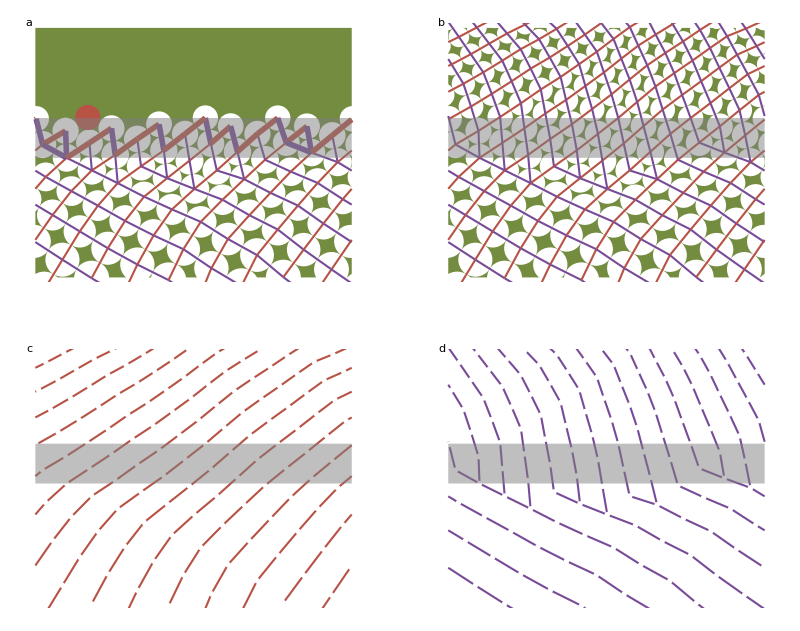

```mathematica
scpDeterministicTransition
```

```mathematica
jExport[scpDeterministicTransition]
```

-Graphics-

### 8 fig:scpParastichyCountsTo55

```mathematica
chainStatistics[run_] := Module[{res,runChains,chainRadii,chainZ},
res=run;
runChains =res["RunChains"];
runChains  = Map[Append[#,<|"DiskNumbers"-> DeleteDuplicates[DiskStacking`bareNumber/@ VertexList[#Chain]]|>]&,runChains];
chainRadii[chain_] := Map[DiskStacking`diskR[res["DiskData"][#]["Disk"]]&,chain["DiskNumbers"]];
chainZ[chain_] := Mean@Map[DiskStacking`diskZ[res["DiskData"][#]["Disk"]]&,chain["DiskNumbers"]];
runChains  = Map[Append[#,<|"MeanZ"-> chainZ[#] |>]&,runChains];
runChains  = Map[Append[#,<|"MeanRadius"-> Mean[chainRadii[#] ]|>]&,runChains];
runChains = Map[KeyDrop[#,"Chain"]&,runChains];
res["RunChains"]=runChains;
res
];

pt[chain_] :={ {paraColours[RGBColor[1, 0, 0]],Point[{1/chain["MeanRadius"],chain["Parastichy"][RGBColor[1, 0, 0]]}]}
,{paraColours[RGBColor[0, 0, 1]],Point[{1/chain["MeanRadius"],chain["Parastichy"][RGBColor[0, 0, 1]]}]}
};

showParaTransitions[oChains_] := Module[{},
Legended[Graphics[{PointSize[Small],Map[pt,Values[oChains]]},
Ticks->{Automatic,Prepend[Table[Fibonacci[n],{n,7,11}],1]},
AxesLabel->{"Radius^-1","Parastichy"},AxesStyle->{jFont[12],jFont[12]},
Axes->True,BaseStyle->jFont[12]
],Placed
[SwatchLegend[Directive[EdgeForm[None],FaceForm[paraColours[#]]]&/@{RGBColor[1, 0, 0],RGBColor[0, 0, 1]},{"Left parastichy count","Right parastichy count"},
LabelStyle->jFont[12]
],{0.25,0.8}]
]
];

(*chainRadiiPlot[runChains_] :=
ListPlot[Map[KeyTake[#,{"MeanZ","MeanRadius"}]&,runChains]];*)
```

```mathematica
upto89=getRunByTag["scp-upto89-solo1"]["Run"];
upto89RunChains = chainStatistics[upto89]["RunChains"];
```

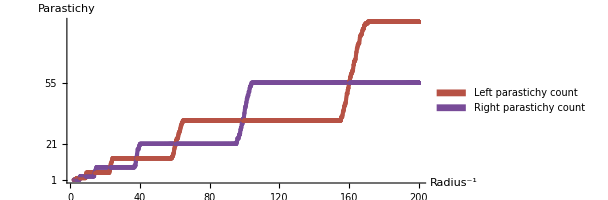

```mathematica
scpParastichyCountsTo89 = showParaTransitions[upto89RunChains];
jExport[scpParastichyCountsTo89]
```

## 6 fig : scpConeTransformation runs but wrong

## Broken Fig 15 Restart after 55

### Restart after 55

```mathematica
If[MemberQ[runsToGenerate,"scpe55-c"],
upto55=getRunByTag["scp-upto55-solo1"]["Run"];
r55c=restartRun[upto55,0.1,1/4,2];
e55c=DiskStacking`executeRun[r55c];
Export[FileNameJoin[{runDirectory,"scp-e55c.mx"}],e55c]
];
```

### Show

```mathematica
debugGraph[g_] := Module[{res,nodes,edges,vc,es},
nodes= VertexList[g];
edges= EdgeList[g];
vc= Association@Map[#->AnnotationValue[{g,#},VertexCoordinates]&,nodes];
es= Association@Map[#->AnnotationValue[{g,#},EdgeStyle]&,edges];
Graph[nodes,edges,VertexCoordinates->Normal[vc],EdgeStyle->Normal[es]]
]

runToMappedGraph[run_,runMappingFunction_] := Module[{dzToDisk,g,vc},
g= debugGraph[run["ContactGraph"]];


vc=Association@Map[#->AnnotationValue[{g,#},VertexCoordinates]&,VertexList[g]];
vc= Normal@Map[runMappingFunction,vc];
AnnotationValue[g,VertexCoordinates]=vc;
AnnotationValue[g,EdgeStyle] = AnnotationValue[g,EdgeStyle]/. {Red->paraColours[Red],Blue->paraColours[Blue]};

g=Graph[g,VertexSize->Tiny,VertexStyle->Directive[EdgeForm[None],FaceForm[None]]];
g
];



dzToDisk[{d_,z_},{zMin_,zMax_},{capOuterRadius_,capInnerRadius_}] := Module[{θ,ρ},
θ= 2 π d;
ρ= capOuterRadius- (z-zMin)/(zMax-zMin) * (capOuterRadius-capInnerRadius);
ρ*{Cos[θ],Sin[θ]}
];

runMapping[run_,zRange_,rRange_] := Module[{zMin,zMax,rMin,rMax,capOuterRadius,capInnerRadius},
{zMin,zMax}= MinMax[diskZ[#Disk]&/@ run["DiskData"]];
{zMin,zMax}= zRange;
{rMin,rMax}=  MinMax[diskR[#Disk]&/@ run["DiskData"]];
{rMin,rMax}= rRange;
capOuterRadius = 1;
capInnerRadius = capOuterRadius*(rMin/rMax);
Function[{dz},dzToDisk[dz,{zMin,zMax},{capOuterRadius,capInnerRadius}]]
];

edgesNotOfStyle[g_,styles_] := Module[{},
Select[EdgeList[g],!MemberQ[styles,AnnotationValue[{g,#},EdgeStyle]]&]
]

asymShow[run_,zRange_,voronoiRange_] := Module[{prunedRun},
prunedRun = DiskStacking`pruneRun[run,zRange];
g1=scpExplain[prunedRun,zRange,{"Circles","Disks","Contacts"},{},Missing[],Missing[]];
g2= grainLines[prunedRun,jParastichyColour[2],zRange,{},Missing[]];
g3= grainLines[prunedRun,jParastichyColour[1],zRange,{},Missing[]];
g123 = GraphicsRow[{g1,g2,g3}];
gshow[graph_] := Show[Graph[graph],Graphics[{FaceForm[None],EdgeForm[Gray],Disk[{0,0},1]}]];
rRange=  MinMax[diskR[#Disk]&/@ prunedRun["DiskData"]];

runMappingFunction =  runMapping[prunedRun,zRange,rRange];
graph = runToMappedGraph[prunedRun,runMappingFunction];
g4=gshow[EdgeDelete[graph,edgesNotOfStyle[graph,{paraColours[Blue],Blue}]]];
g5=gshow[EdgeDelete[graph,edgesNotOfStyle[graph,{paraColours[Red],Red}  ]]];

graphVoronoi = runToMappedGraph[ DiskStacking`pruneRun[run,voronoiRange],runMappingFunction];
g6= Show[showDiskMeshFromNodes[graphVoronoi],Graphics[{FaceForm[White],Disk[{0,0},First[runMappingFunction[{0,18}]]]}]];
g45 = GraphicsRow[{g6,g4,g5}];
GraphicsColumn[{g123,g45}]
];
```

```mathematica
e55c=getRunByTag["scp-e55c"]; 
scpFalling = asymShow[run=e55c,zRange={17.5,18},voronoiRange={17,18.5}];
jExport[scpFalling]
```

-Graphics-

```mathematica
showDiskMeshFromNodes[g_] := Module[{gstyle,nodes,vx,mask},
nodes=AnnotationValue[g,VertexCoordinates];
v=VoronoiMesh[nodes];
v=Region[Style[v,EdgeForm[Black],FaceForm[None]]];
mask= DiscretizeRegion@RegionDifference[Rectangle[{-2,-2},{2,2}],Disk[]];
mask=Region[Style[mask,White]];
gstyle=Graph[g,VertexSize->Large,VertexStyle->Gray];
Show[gstyle,v,mask,PlotRange->{{-1,1},{-1,1}}]
];
```

```mathematica
pars55b =<|"Tag"->"scp-past55-b","rSlope"->0.1,"rScale"->60,
"FallingFunction"-><|"rSlope"->0.1,"rScale"->40,"Power"->1/2|>
,"PostFixChains"->2,
"Noise"->0,
"Lattice"->LatticePhyllotaxis`latticeOrthogonal[{0,1},{0,2}]|>;
pars55b =<|"Tag"->"scp-past55-b","rSlope"->0.1,"rScale"->60,
"FallingFunction"-><|"rSlope"->0.1,"rScale"->40,"Power"->1/2|>
,"PostFixChains"->2,
"Noise"->0,
"Lattice"->LatticePhyllotaxis`latticeOrthogonal[{0,1},{0,2}]|>;
If[MemberQ[runsToGenerate,"past55-b"],
past55b = DiskStacking`executeRun[readyRunFromParameter[pars55b]];
Export[FileNameJoin[{runDirectory,"scp-past55-b.mx"}],past55b]
];
```

```mathematica
(*

runDiskTransform :=diskTransform[stemParameters["zUpperRim"],stemParameters["zMax"]];
runDiskTransformXY[dz_] := Take[runDiskTransform[dz],2];

runConeTransform[{d_,z_}] :=  Module[{},
Which[
z<stemParameters["zLowerRim"], coneTransform[stemParameters["zLowerRim"],stemParameters["coneSlope"]][{d,z}],
z<stemParameters["zUpperRim"], 
 {Cos[2π d],Sin[2 π d],z}
,(*z<stemParameters["zMax"]*) True, runDiskTransform[{d,z}]
]
];
*)
```

```mathematica
(*
topPlug ={CapForm["Butt"],Tube[{{0,0,stemParameters["zUpperRim"]-0.1},{0,0,stemParameters["zUpperRim"]+0.01}},0.4]};

coneGraphics3D[run_,transform_] := Module[{graph,nodes,vMesh,colouredNodes,lp,contactLines,coneContactLines,g3},
graph= run["ContactGraph"];
nodes=AnnotationValue[graph,VertexCoordinates];
colouredNodes= Map[{xStyle[nodeType[#]],Point[transform[#]]}&,Select[nodes,!(MissingQ[nodeType[#]]
|| nodeType[#]=="Inner seeds") &]];

vMesh= voronoiMeshNoEdge[AnnotationValue[graph,VertexCoordinates],stemParameters["voronoiMeshZRange"] ];
lp=meshToTransformedGraphics[vMesh,transform];


contactLines= Last/@Select[graphToContactLines[coneRun,leftRightColours],First[#]==RGBColor[0.7194116276462343, 0.32145384723880266, 0.27090344303450226]&];
coneContactLines ={RGBColor[0.7194116276462343, 0.32145384723880266, 0.27090344303450226],Map[meshToTransformedGraphics[#,transform]["Lines"]&,contactLines]};

g3=Graphics3D[{
{EdgeForm[None],FaceForm[White],lp["Polygons"]}
,lp["Lines"],topPlug,
{Thick,coneContactLines},{PointSize[Large],colouredNodes}},Lighting->"Neutral",ViewPoint->{1.15,-2.99,1.06},Boxed->False,Method->{"ShrinkWrap" -> True}];
g3
];



voronoiMeshNoEdge[nodes_,zRange_] := Module[{overlap,wrap,vMesh,cellSelector},
overlap=0.2;
wrap= Join[nodes,Map[ {#[[1]]+1,#[[2]]}&,Select[nodes,#[[1]]<=-0.5+overlap&]],Map[ {#[[1]]-1,#[[2]]}&,Select[nodes,#[[1]]>0.5-overlap&]]];
vMesh= VoronoiMesh[wrap,{{-1/2-overlap,1/2+overlap},zRange}];
cellSelector= Map[RegionWithin[Rectangle[{-1/2-overlap/2,zRange[[1]]},{1/2+overlap/2,zRange[[2]]}],#]&,MeshPrimitives[vMesh,2]];
vMesh=MeshRegion[MeshCoordinates[vMesh],Pick[MeshCells[vMesh,2],cellSelector]];
vMesh
];
*)
```

```mathematica
(*past55b=getRunByTag["scp-past55-b"];
run=past55b;
arena= makeRfunction[run["Arena"]];
stemParameters= KeyTake[arena,{"zMin","zLowerRim",
"zUpperRim","zMax"}];
stemParameters["coneSlope"]=0.5;
stemParameters["zMax"]=5.25; (* matters! *)
stemParameters["zCutoff"]=5.15; 
stemParameters["voronoiMeshZRange"] = {4.2,stemParameters["zCutoff"]};
coneRun= pruneRun[run,{4.2,5.2}];
diskRun=DiskStacking`pruneRun[run,{stemParameters["zUpperRim"],5.2}];
diskRun=DiskStacking`pruneRun[run,{4.6,5.2}];
stackRun = DiskStacking`pruneRun[run,{3,5.2}];
*)
```

```mathematica
(*{a,b,c}={diskGraphics[diskRun,runDiskTransformXY],coneGraphics3D[coneRun,runConeTransform],stackGraphics[stackRun]};
b6=Show[b,ImageSize->600];a3=Show[a,ImageSize->300];c3=Show[c,ImageSize->300];
scpConeTransformation = Grid[{{b6,SpanFromLeft},{a3,c3}},Frame->None];
jExport[scpConeTransformation]*)
```

Interrupted

```mathematica
stackGraphics[run_]:= Module[{disks,diskStyle,contactLines},
disks=Values[Map[#Disk&,run["DiskData"]]];
diskStyle[p:Disk[xz_,r_]] := {xStyle[nodeType[xz]],p};
contactLines= {RGBColor[0.7194116276462343, 0.32145384723880266, 0.27090344303450226],Last/@Select[graphToContactLines[run,leftRightColours],First[#]==RGBColor[0.7194116276462343, 0.32145384723880266, 0.27090344303450226]&]};
 Graphics[{ffs,diskStyle/@disks,{contactLines}},PlotRange->{{-1/2,1/2},{4.3,5.1}},PlotRangeClipping->True]
];
```

```mathematica
diskGraphics[run_,transform_] := Module[{g,g2,lp,nodes,zRange,vMesh,runDiskTransform,colouredNodes},
g=run["ContactGraph"];
nodes=AnnotationValue[g,VertexCoordinates];
vMesh= voronoiMeshNoEdge[nodes,{stemParameters["zUpperRim"],stemParameters["zCutoff"]}];
lp=meshToTransformedGraphics[vMesh,transform];

colouredNodes= Map[{xStyle[nodeType[#]],PointSize[Medium],Point[transform[#]]}&,Select[nodes,!(MissingQ[nodeType[#]]
|| nodeType[#]=="Inner seeds") &]];

contactLines= Last/@Select[graphToContactLines[run,leftRightColours],First[#]==RGBColor[0.7194116276462343, 0.32145384723880266, 0.27090344303450226]&];
diskContactLines ={RGBColor[0.7194116276462343, 0.32145384723880266, 0.27090344303450226],Map[meshToTransformedGraphics[#,transform]["Lines"]&,contactLines]};

g2=Graphics[{
{EdgeForm[None],FaceForm[White],lp["Polygons"]}
,lp["Lines"],diskContactLines,{FaceForm[White],Disk[{0,0},0.4]},
colouredNodes},Method->{"ShrinkWrap" -> True}];
g2
];
```

```mathematica
nodeType[{x_,z_}] := 
Which[
z<stemParameters["zLowerRim"],"Undeveloped"
,z<stemParameters["zUpperRim"], "Bract"
,z<5, "Ray floret"
,z<5.15,"Seeds"
,z<stemParameters["zMax"],"Inner seeds"
, True, Missing[]
];
```

```mathematica
yellow3D=Darker[Yellow,0.1];
blackEdged[colour_] := Directive[EdgeForm[Black],FaceForm[colour],colour]
xSwatch = <|"Seeds"->blackEdged@ColorData["CoffeeTones"][0.3],
"Inner seeds"->(*ColorData["CoffeeTones"][0.1]*)Red
,"Ray floret"->blackEdged[yellow3D]
,"Bract"-> blackEdged@jParastichyColour[3]
,"Undeveloped"-> (*ColorData["GrayYellowTones"][0.5]*) Directive[EdgeForm[Black],FaceForm[None],Black]
|>;

xStyle[nodeLabel_] := Directive[{If[!MissingQ[xSwatch[nodeLabel]],xSwatch[nodeLabel],Black],
Switch[nodeLabel,"Ray floret" | "Bract",PointSize[Large],
___,Nothing[],Missing[___],Nothing[]]}]
```

```mathematica
coneTransform[zLowerRim_,coneSlope_][{d_,z_}] := Append[(1- (zLowerRim-z)*coneSlope)*{Cos[2π d],Sin[2 π d]},z
];

diskTransform[zUpperRim_,zMax_][{d_,z_}] := 
Module[{r},
r=1- (z-zUpperRim)/(zMax-zUpperRim);
Append[r*{Cos[2π d],Sin[2 π d]},zUpperRim
]
];
```

```mathematica
polygonTransform[Polygon[poly___],transform_] := (Polygon[Map[transform,poly]]);
lineTransform[Line[line___],transform_] := (Line[Map[transform,line]]);
```

```mathematica
ffs= Directive[FaceForm[None],EdgeForm[Gray]];
```

```mathematica
meshToTransformedGraphics[vMesh_,transform_] := Module[{lMesh,lMesh2,lines2,lines3,rmesh,polys2,polys3},
lMesh = MeshRegion[MeshCoordinates[vMesh],MeshCells[vMesh,1]];
lMesh2= DiscretizeRegion[lMesh,MaxCellMeasure->{"Length"->.005}];
lines2= MeshPrimitives[lMesh2,1];
lines3= lineTransform[#,transform]&/@lines2;
rmesh =DiscretizeRegion[vMesh,MaxCellMeasure->{"Length"->.01}];polys2= MeshPrimitives[rmesh,2];
polys3= Map[polygonTransform[#,transform]&,polys2];
<|"Lines"->lines3,"Polygons"->polys3|>
];
```

## 7 fig:scpMOSIhistogram

from  textbook  code

```mathematica
countMOSI = {89,89,89,89,89,55,74,89,55,89,53,54,34,89,55,55,34,55,21,55,34,41,55,88,36,29,42,21,18,34,55,89,55,89,55,89,76,89,83,55,55,55,78,55,88,89,89,144,89,89,93,55,89,89,88,55,89,89,68,89,89,34,55,89,76,34,54,89,144,55,55,88,55,89,73,89,68,89,88,86,90,143,110,89,143,142,144,144,89,89,89,89,34,21,79,55,88,34,54,47,48,50,89,54,89,59,55,68,55,55,55,76,89,55,55,47,89,55,89,33,35,43,57,20,19,55,40,89,89,47,55,34,53,84,89,89,89,89,55,34,34,34,54,55,55,55,55,89,89,55,55,55,55,55,55,55,87,123,33,55,89,55,55,143,89,55,53,89,89,76,54,21,33,47,32,55,49,89,76,55,55,89,68,55,89,34,55,56,57,89,53,89,55,88,55,55,55,55,55,34,55,55,55,55,34,34,55,144,76,34,55,89,55,89,34,55,55,55,76,144,19,57,21,34,55,89,89,68,89,89,55,89,88,89,88,50,89,89,89,55,75,88,55,34,89,89,54,89,89,89,89,55,55,55,55,34,34,144,54,89,88,55,55,89,89,55,89,55,55,55,86,89,54,86,89,55,73,89,80,34,55,89,34,89,53,89,55,89,89,55,34,55,34,55,55,55,68,89,55,34,89,55,68,77,47,55,55,55,55,55,54,47,89,55,34,54,55,88,34,55,47,55,55,34,55,55,55,55,55,74,89,54,89,55,55,55,55,55,55,55,55,42,55,54,55,55,68,55,55,55,54,55,55,55,47,55,55,55,55,68,55,55,55,47,55,55,88,50,89,112,89,89,89,89,89,55,68,55,55,55,55,55,55,62,44,29,55,89,89,55,55,34,55,34,34,34,89,75,87,52,55,55,55,56,55,34,55,34,53,34,36,21,55,34,21,34,20,34,21,25,34,55,21,20,26,13,21,34,55,36,55,34,55,47,55,49,35,34,47,34,55,55,89,55,57,34,55,55,55,34,55,55,42,55,55,22,34,55,47,21,34,55,89,34,34,55,34,55,45,55,42,55,54,54,89,68,55,90,89,89,89,55,55,55,55,21,47,55,21,34,29,48,55,55,55,42,34,34,34,47,55,34,34,29,55,34,55,21,21,29,33,13,34,55,55,28,34,34,54,55,55,55,55,34,21,21,21,34,34,34,34,55,54,34,34,34,34,34,34,55,76,19,35,55,34,34,88,55,34,35,55,55,47,36,13,21,29,34,32,56,47,36,34,55,42,34,55,21,34,54,56,34,55,34,34,34,34,34,21,34,34,34,34,21,21,34,47,21,34,55,34,55,34,34,34,47,89,18,34,13,21,34,55,55,42,55,55,34,54,55,55,55,55,55,55,34,48,34,21,55,56,35,55,55,55,55,34,34,36,34,21,21,89,34,55,55,34,34,55,55,55,34,34,34,56,54,34,55,56,34,55,55,68,21,34,55,21,55,34,55,55,34,21,34,34,34,34,42,54,34,21,54,34,56,29,34,34,34,34,34,34,29,55,34,21,34,34,55,21,34,29,34,34,34,34,34,34,34,46,55,34,55,36,35,38,37,34,34,34,34,27,34,34,34,33,42,34,34,34,34,34,34,34,29,34,34,34,34,42,34,36,34,29,34,34,55,31,55,69,55,55,55,55,55,34,42,34,34,34,34,34,34,31,28,34,54,55,34,34,21,34,21,21,21,55,47,52,31};

fType[x_] := Which[
MemberQ[{13,21,34,55,89,144}-1,x],"Fibonacci ±1",
MemberQ[{13,21,34,55,89,144}+1,x],"Fibonacci ±1",
MemberQ[{1,4,5,9,14,23,37,60,97},x],"F4",
MemberQ[{1,3,4,7,11,18,29,47,76,123},x],"Lucas",
MemberQ[{2,4,6,10,16,26,42,68,110},x],"Fibonacci x2",
MemberQ[{1,2,3,5,8,13,21,34,55,89,144},x],"Fibonacci",
True,"Other"
];


scpPalette = <|
"Fibonacci"->Directive[FaceForm[None],EdgeForm[jStyle["ParastichyColour"][1]]]
,"Fibonacci x2"-> jStyle["ParastichyColour"][2]
,"Lucas"-> jStyle["ParastichyColour"][3]
,"F4" -> Directive[FaceForm[ jStyle["ParastichyColour"][4]],EdgeForm[{Black}]]
,"Fibonacci ±1"-> jStyle["ParastichyColour"][5]
,"Other"-> jStyle["CylinderColour"]
|>;
bar[{spirals_,observed_}] := Module[{barColour},
barColour = scpPalette[fType[spirals]];
{barColour,Rectangle[ {spirals-0.45,0},{spirals+0.45,observed}]}
];

alabel ={"Parastichy number"," Seen"};
alabel = None;
legend =SwatchLegend[Values[scpPalette],Keys[scpPalette],LabelStyle->Directive[FontFamily-> jStyle["FontFamily"],FontSize->Scaled[0.02]]];
fticks = {{Automatic,None},{Automatic,{21,34,55,89,144}}};
frame ={{True,True},{True,True}};
fsize= Scaled[0.05];
scpHistogram1 :=Graphics[
{Map[bar,Tally[countMOSI]]},
Axes->True,
FrameTicks->fticks,AxesOrigin->{10,0},AspectRatio->1,
FrameLabel->alabel,Frame->frame,
LabelStyle->Directive[FontFamily-> jStyle["FontFamily"],FontSize->fsize]];
```

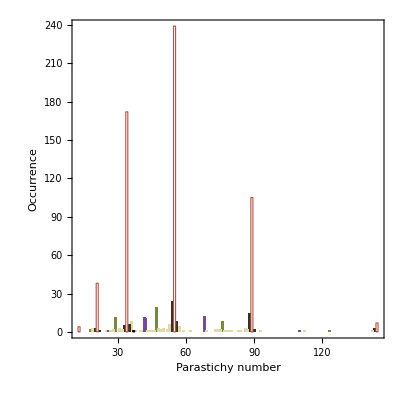

```mathematica
scpMOSIHistogram:= Legended[Show[scpHistogram1,FrameLabel->{"Parastichy number","Occurrence"}],legend];
jExport[scpMOSIHistogram]
```

## 9 & 10 runs to redo fig:scpTo55 and fig:scpAha, fig:scpDouble and fig:scpLucas Histograms up to 55

```mathematica
makeUpto55wxy := Module[{},
replicationCount=10;
noises =Join[{0},Table[0.01,replicationCount],Table[0.02,replicationCount],Table[0.05,replicationCount],Table[0.1,replicationCount]];
parsets = expandParameterSets[<|"Tag"->{"scp-upto55-wxy"},"rSlope"-> {0.01,0.03,0.07,0.1,0.2,0.3},"rScale"->{60},"PostFixChains"->{10},
"Noise"->noises
,"Lattice"-> {LatticePhyllotaxis`latticeOrthogonal[{0,1},{0,2}]}|>];
doRunSets[parsets]
];
```

### Exploring up to 55

```mathematica
extractupto55 := (
upto55wxyFiles =FileNames[FileNameJoin[{runDirectory,"scp-upto55-wxy*.mx"}]];
upto55Results= Monitor[Map[runExtractNonOverlappingChains,upto55wxyFiles],monitorFile];
groupedupto55Results =GroupBy[upto55Results,KeyTake[#["Arena"],{"rSlope","Noise"}]&];
Export[FileNameJoin[{eSetDirectory,"scp-esetupto55-wxy.mx"}],groupedupto55Results];
);
```

```mathematica
groupedupto55Results=Import[FileNameJoin[{eSetDirectory,"scp-esetupto55-wxy.mx"}]];
upto55Show = KeySelect[groupedupto55Results,#rSlope< 0.15&];
```

```mathematica
histogramOverRun[run_] :=Module[{counts},
counts =Flatten[Values/@Values[run["ChainParastichies"]]];
counts= Flatten@ Normal[counts];
counts=GroupBy[counts, First->Last ,Total];
counts
];
histogramOverRuns[runList_] := Module[{counts},

counts=Map[histogramOverRun,runList];
counts =Flatten[Normal/@counts];
counts=GroupBy[counts, First->Last ,Total];
counts 
];
paraScaling[x_] := Log10[1+x];
paraScaling[x_] := x;
paraScaling[x_] := Log10[1+x];


countStyling[count_] := scpPalette[fType[count]];

histogramBars[runList_] :=  Module[{counts,bars},
If[MissingQ[runList],Return[{}]];
counts=histogramOverRuns[runList];
counts = N@ counts/Total[counts];
counts = paraScaling/@counts;
bars=KeyValueMap[{countStyling[#],Rectangle[{#1-0.4,0},{#1+0.4,#2}]}&,counts]
];
histogram[runList_] :=  Module[{counts},
Graphics[{jParastichyColour[1]
,histogramBars[runList]}
,PlotRange->{{12,56},{0,0.07}}
,PlotRangeClipping->True
,PlotRangePadding->None
,Ticks->{{13,21,34,55},None}
,BaseStyle->jFont[10]
,Axes->{True,False}
,AspectRatio->1
,Background->Lighter[Gray, 0.9]
]

];
```

```mathematica
panelEset[eset_] := Module[{noises,slopes,hpanel,titlerow,noiserow,changerow,panels},
noises= Sort@DeleteDuplicates@Map[#Noise&,Keys[eset]];
slopes = Sort@DeleteDuplicates@Map[#rSlope&,Keys[eset]];
hpanel[noise_,slope_] := Module[{res,highlight},
res=eset[<|"rSlope"->slope,"Noise"->noise|>];
highlight=(slope==0.03 && noise ==0.05);
res=Item[histogram[res],Background->If[highlight,Gray,None]];
res
];
hpanel[slope_] := Join[{slope},Map[hpanel[#,slope]&,noises]];
titlerow= {"","Noise σ",Splice[Table[SpanFromLeft,Length[noises]]]};
noiserow= Join[{""},Map[Item[#,Frame->{True,False,False,False}]&,noises]];
changerow= {"Disk change r" <> FromCharacterCode[39]};
panels = Grid[
Join[{titlerow,noiserow,changerow},Map[hpanel,slopes]]
,BaseStyle->jFont[12],Spacings->{.2,0}
]
];
```

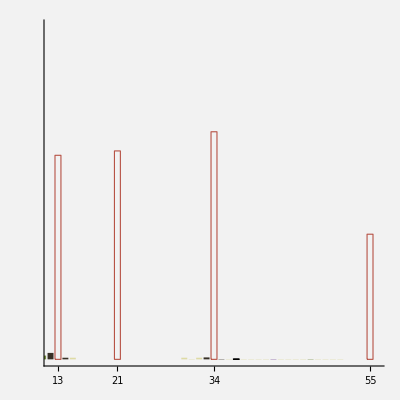
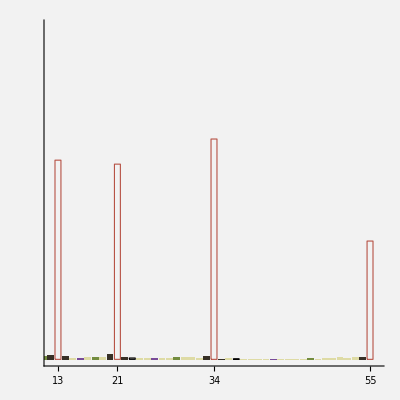
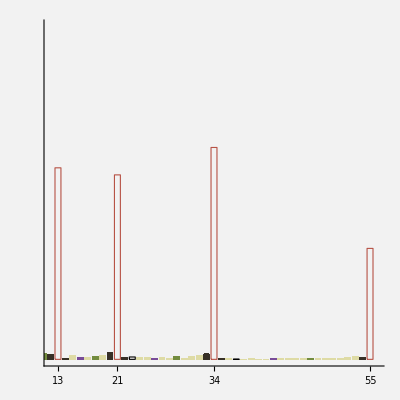
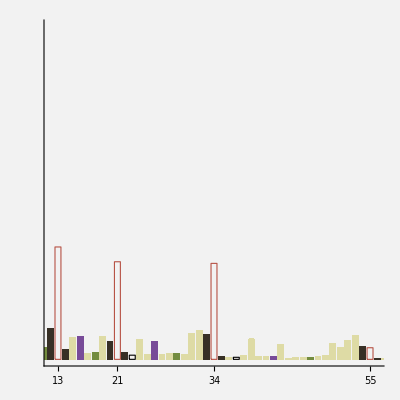
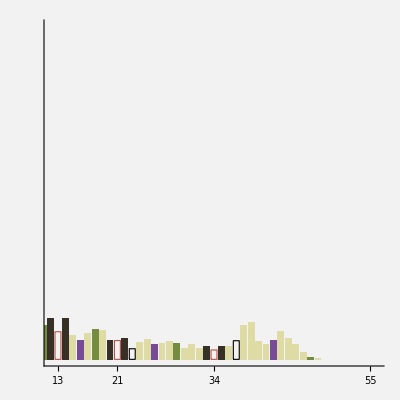
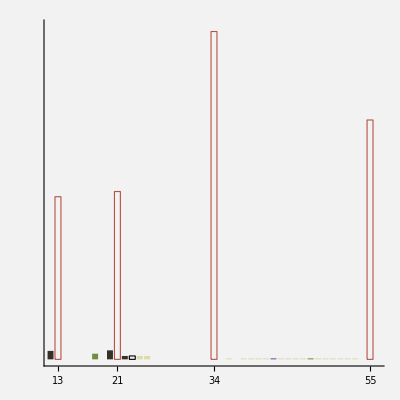
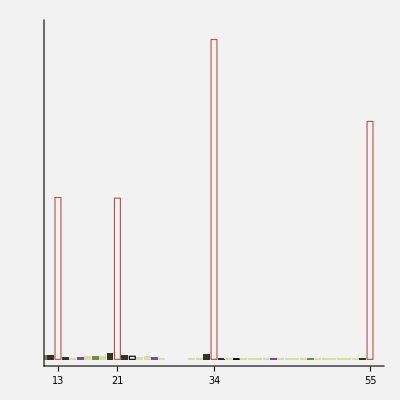
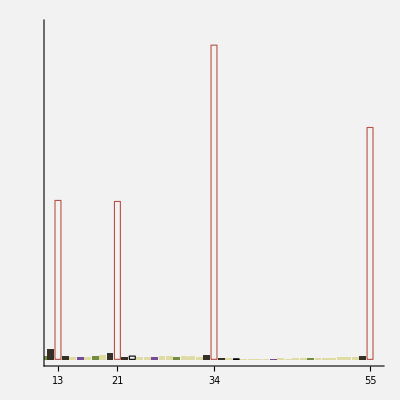
| Noise σ |  |  |  |  | 
 | 0 | 0.01 | 0.02 | 0.05 | 0.1 | 
Disk change r' |  |  |  |  |  | 
0.01 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
0.03 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
0.07 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
0.1 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
scpTo55 = panelEset[upto55Show];
jExport[scpTo55]
```

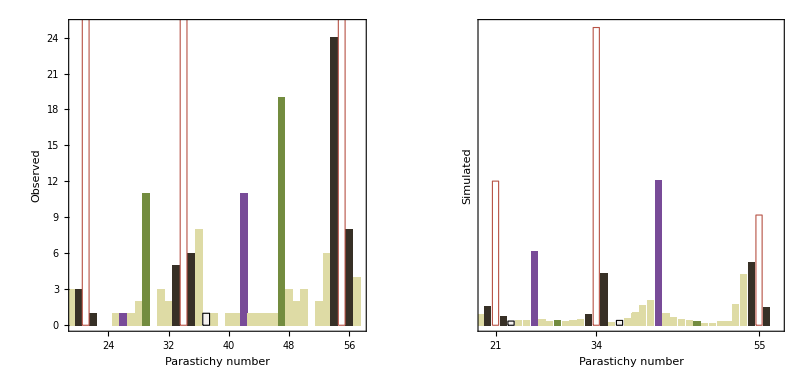

```mathematica
ahaRun= upto55Show[<|"rSlope"->0.03,"Noise"->0.05|>] ;
scpAha = Legended[
Show[histogram[ahaRun],Axes->{True,True},PlotRange->{{10,55},{0,0.04}},FrameLabel->{"Parastichy number","Frequency"},Frame->True,FrameTicks->{Automatic,Automatic},Background->None]
,Placed[legend,Right]];

xRange={19.5,57.5};
g2 = Graphics[
{Map[bar,Tally[countMOSI]]},
Axes->True,
AxesOrigin->{20,0},AspectRatio->1,PlotRangeClipping->True,
FrameLabel->{"Parastichy number","Observed"},Frame->frame,
BaseStyle->jFont[12],
PlotRange->{xRange,{0,25}}];
scpAhaPair = Legended[GraphicsRow[{g2,
Show[histogram[ahaRun],Axes->{True,True},PlotRange->{xRange,{0,0.04}},FrameLabel->{"Parastichy number","Simulated"},Frame->True,
BaseStyle->jFont[12],Background->None]
}],Placed[legend,Right]];
jExport[scpAhaPair]
```

## 11 & 12 fig: scpDet813 and fig:scpSch813

```mathematica
histobars[counts_] := KeyValueMap[{grainCountStyling[#1],Rectangle[{#1-0.4,0},{#1+0.4,#2}]}&,counts/Total[counts]];
paraScaling[x_] := Log10[1+x];
paraScaling[x_] := x;
textSize = jFont[9];
clabel[run_] := StringTemplate["r':`rSlope` σ: `Noise`"][run["Arena"]]

grainCountStyling[count_] := scpPalette[fType[count]];

parastichyCounts[run_,col_] := Module[{paras,counts,clook},
paras=Map[#Parastichy&,run["RunChains"]];
If[col==={RGBColor[0, 0, 1],RGBColor[1, 0, 0]},
counts= Flatten@Values[Values /@ paras];
counts= Counts[counts]
,
clook= If[col==RGBColor[0, 0, 1],clook=RGBColor[1, 0, 0],clook=RGBColor[0, 0, 1]];
counts =Counts[Map[#[clook]&,paras]]
];
counts=paraScaling/@counts;
counts 
];
parastichyBars[run_,col_] := Module[{counts,bars},
counts =parastichyCounts[run,col]; 
bars= histobars[counts];
bars
]
parastichyBarGraph[run_,hRange_,col_] := Module[{g,axis},
If[Length[col]==0,
g={};axis=Transparent
,
g=parastichyBars[run,col];axis=Black];
Graphics[g,Axes->{True,False}
,AxesStyle->axis
,PlotRange->{hRange,{0,paraScaling[1]}},AspectRatio->1/2,
Ticks->{{5,8,13,21},{None}},
BaseStyle->textSize]
];
pcolumn[run_,hRange_,zRange_,col_] := GraphicsColumn[{
 parastichyBarGraph[run,hRange,col],
grainLines[run,paraColours[col],zRange,{}]
},Frame->None]
grainShow[run_,hRange_,zRange_] := GraphicsColumn[{clabel[run],GraphicsRow[{pcolumn[run,hRange,zRange,RGBColor[0, 0, 1]],pcolumn[run,hRange,zRange,RGBColor[1, 0, 0]]},Frame->None]},BaseStyle->textSize]
```

### scpDet813

```mathematica
makescpDet813 := (
(*d813= makeParameterSets[<|"Tag"->{"scp-d813-a"},"rSlope"->{0.1,0.5,1},"rScale"->{1.6},"PostFixChains"->{20},
"Noise"->{0},
"Lattice"-> {LatticePhyllotaxis`latticeOrthogonal[{8,13},{0,.4}]}|>];
*)
d813b= expandParameterSets[<|"Tag"->{"scp-d813-b"},"rSlope"->{0.05,0.1,0.5,1},"rScale"->{1.6},"PostFixChains"->{20},
"Noise"->{0},
"Lattice"-> {LatticePhyllotaxis`latticeOrthogonal[{8,13},{0,.4}]}|>];
doRunSets[d813b];(*d813c= expandParameterSets[<|"Tag"->{"scp-d813-c"},"rSlope"->{0.01,0.02},"rScale"->{1.6},"PostFixChains"->{20},
"Noise"->{0},
"Lattice"-> {LatticePhyllotaxis`latticeOrthogonal[{8,13},{0,.4}]}|>];
doRunSets[d813c];
*));
```

```mathematica
det813= Map[Import[#]["Run"]&,FileNames[FileNameJoin[{runDirectory,"scp-d813-b*"}]]];
showZBar=True;
contactLineThickness=AbsoluteThickness[0.5];
textSize= jFont[12];
paraScaling[x_] := Log10[1+x];
scpDet813=  GraphicsGrid[Partition[grainShow[#,{7,22},{0,2}]&/@det813,2]];
```

$Aborted

```mathematica
jExport[scpDet813]
```

-Graphics-

### scpSCH813

```mathematica
(* no replication here for example runs *)
pGHQ= expandParameterSets[<|"Tag"->{"scp-GHQ"},"rSlope"->{0.1,0.5,1},"rScale"->{1.6},"PostFixChains"->{20},
"Noise"->{0.02,0.1},
"Lattice"-> {LatticePhyllotaxis`latticeOrthogonal[{8,13},{0,.4}]}|>];
(*doRunSets[pGHQ];
*)
```

G:\My Drive\Work\Textbook\Stacked coin paper\Mathematica\Runs\scp-GHQ1.mx

G:\My Drive\Work\Textbook\Stacked coin paper\Mathematica\Runs\scp-GHQ2.mx

G:\My Drive\Work\Textbook\Stacked coin paper\Mathematica\Runs\scp-GHQ3.mx

G:\My Drive\Work\Textbook\Stacked coin paper\Mathematica\Runs\scp-GHQ4.mx

G:\My Drive\Work\Textbook\Stacked coin paper\Mathematica\Runs\scp-GHQ5.mx

G:\My Drive\Work\Textbook\Stacked coin paper\Mathematica\Runs\scp-GHQ6.mx

```mathematica
(* 
makeFiles= Map[doOneRunNoPP,pGH];
makeFiles= Map[doOneRunNoPP,pGHQ];
*)
```

```mathematica
ghqFiles = FileNames[FileNameJoin[{runDirectory,"scp-GHQ*.mx"}]];
ghqRuns= Map[Import[#]["Run"]&,ghqFiles];
paraScaling[x_] := x;
gsch=Partition[grainShow[#,{7,22},{0,2}]&/@ghqRuns,2];
scpSch813=GraphicsGrid[gsch];
jExport[scpSch813]
```

-Graphics-

## 13 fig:scpColumn

```mathematica
grainColShow[run_,hRange_,zRange_] := GraphicsColumn[{GraphicsRow[
{pcolumn[run,hRange,zRange,RGBColor[0, 0, 1]],pcolumn[run,hRange,zRange,RGBColor[1, 0, 0]]
,qcolumn[run,hRange,zRange,Missing[]]},Frame->None]},BaseStyle->textSize];
qcolumn[run_,hRange_,zRange_,dRange_] := Module[{r},
If[MissingQ[dRange],r={},r=Rectangle[{dRange[[1]],zRange[[1]]},{dRange[[2]],zRange[[2]]}]];
GraphicsColumn[{
 parastichyBarGraph[run,hRange,{RGBColor[0, 0, 1],RGBColor[1, 0, 0]}],
Show[scpExplain[run,{0,2},{"Disks","Contacts"},{},Missing[],Missing[]]
,Graphics[{FaceForm[Opacity[0.1],Gray],r}]]
},Frame->None]
];
zColumn[run_,hRange_,zRange_,dRange_] := GraphicsColumn[{
 parastichyBarGraph[run,hRange,{}],
Show[scpExplain[run,{0,2},{"Disks","Contacts"},{},Missing[],Missing[]],
PlotRange->{dRange,zRange}]
},Frame->None];
```

```mathematica
pQSS= expandParameterSets[<|"Tag"->{"scp-QSS"},"rSlope"->{0.1},"rScale"->{1.6},"PostFixChains"->{20},
"Noise"->{0.1},
"Lattice"-> {LatticePhyllotaxis`latticeOrthogonal[{8,13},{0,.4}]}|>];
(* this is the same as one of the GHQ runs...*)
doRunSets[pQSS]
```

G:\My Drive\Work\Textbook\Stacked coin paper\Mathematica\Runs\scp-QSS1.mx

```mathematica
runQSS= Import[FileNameJoin[{runDirectory,"scp-QSS1.mx"}]]["Run"];
```

```mathematica
scpColumn = grainColShow[runQSS,{12,22},{0,2}];
jExport[scpColumn]
```

-Graphics-

#### unused runDouble

```mathematica
(*runNumberDouble =(First@Select[ahaRun,finalLowerCount[#]==42&])["Arena"]["Run"]
runDouble = Import[FileNameJoin[{runDirectory,"scp-upto55-wxy65.mx"}]]["Run"];scpDouble = scpExplain[runDouble,{5,15},{"Disks","Contacts"},{},Missing[],Missing[]];
jExport[scpDouble]
*)
```